```mathematica
ClearAll[ρ,nrho,rcrho,α,β]
```

```mathematica
ρ[r_,nrho_,rcrho_,α_,β_]=nrho^2 * (r/rcrho)^(-1/2*α) / (1 + (r/rcrho)^2)^(3/2 * β - 1/4*α)
```

nrho^2 (1+r^2/rcrho^2)^(α/4-(3 β)/2) (r/rcrho)^(-α/2)

```mathematica
Manipulate[
LogLogPlot[ρ[r,nrho,rcrho,α,β],{r,0.001,1},PlotRange->{0,1}],
{{nrho,1},0.1,2.0,0.01},
{{rcrho,0.15},0.1,0.2,0.01},
{{α,0.8},0.1,1.0,0.01},
{{β,0.7},0.1,1.0,0.01}
]
```

```mathematica
ClearAll[T,nT,rcT,a,b]
```

```mathematica
T[r_,nT_,rcT_,a_,b_]=nT * (1+a*r/rcT) / ((1+(r/rcT)^2)^b)
```

nT (1+r^2/rcT^2)^-b (1+(a r)/rcT)

```mathematica
Manipulate[
LogLinearPlot[T[r,nT,rcT,a,b],{r,0.01,1},PlotRange->{0,13}],
{{nT,5},5,5},
{{rcT,0.15},0.0,0.3,0.01},
{{a,2.5},0.0,5.0,0.1},
{{b,0.7},0.0,1.4,0.01}
]
```

```mathematica
ClearAll[bovera,a,b,α,β]
```

```mathematica
bovera[a_,α_,β_]=β+a*α
```

a α+β

```mathematica
Manipulate[
Plot[bovera[a,α,β],{a,0.01,1},PlotRange->Automatic],
{{α,-3},-5,5,0.1},
{{β,3},-3,3,0.1}
]
```

```mathematica
Manipulate[
Graphics[Circle[{0,0},{a*(β+a*α),a}]],
{{a,0.5},0,1,0.01},
{{α,-3},-5,5,0.1},
{{β,3},-3,3,0.1}
]
```

```mathematica
ClearAll[a,b,α,β]
```

```mathematica
radii=Table[N[-Log[(13-x)/12]],{x,1,12,1}]
```

{0.,0.0870114,0.182322,0.287682,0.405465,0.538997,0.693147,0.875469,1.09861,1.38629,1.79176,2.48491}

```mathematica
a=radii
```

{0.,0.0870114,0.182322,0.287682,0.405465,0.538997,0.693147,0.875469,1.09861,1.38629,1.79176,2.48491}

```mathematica
b=a*(β+α*a)
```

```mathematica
Manipulate[
Graphics[
Plot[
(1/Exp[α*(Tanh[β*Log[r/0.1]-1])]),
{r,0,2}]],
{{α,1},0,2,0.01},
{{β,-1},-1,-0.1,0.01}
]
```

```mathematica
Manipulate[
Graphics[
Plot[
1/Exp[α*Log[r]+β],
{r,0,1}],
PlotRange->Full],
{{α,0},-1,1,0.01},
{{β,0},-1,1,0.01}
]
```

```mathematica
ClearAll[a,b,α,β]
```

```mathematica
(*radii={0.25,0.4,0.6,0.8,1.};*)
(*radii=Table[x/12,{x,1,12,1}]*)
radii=Table[N[-Log[(13-x)/12]],{x,1,12,1}]
```

{0.,0.0870114,0.182322,0.287682,0.405465,0.538997,0.693147,0.875469,1.09861,1.38629,1.79176,2.48491}

```mathematica
(*Table[Circle[{0,0},{a*(β+a*α),a}],{a,radii}];*)
Table[Circle[{0,0},{a*(β+a*α),a}],{a,radii}];
```

```mathematica
Graphics[%];
```

```mathematica
Manipulate[
Graphics[Table[Circle[{0,0},{a*(β+a*α),a}],{a,radii}],Axes->True],
{{α,2},-5,5,0.1},
{{β,1},-5,5,0.1}
]
```

```mathematica
ClearAll[a,b,α,β,radii]
```

```mathematica
(*radii={0.25,0.4,0.6,0.8,1.};*)
(*radii=Table[x/12,{x,1,12,1}]*)
radii=Table[(1/N[Log[x]]-0.38)/2.086303462376432,{x,1.5,13,1}]
```

{1.,0.340965,0.200467,0.136538,0.0990254,0.073932,0.0557454,0.0418325,0.0307671,0.0217049,0.0141121,0.00763329}

```mathematica
Table[radii[[12-i]],{i,0,12}]
```

{0.00763329,0.0141121,0.0217049,0.0307671,0.0418325,0.0557454,0.073932,0.0990254,0.136538,0.200467,0.340965,1.,List}

```mathematica
radii={0.000763329,0.001526658,0.002289987,0.003053316,0.003816645,0.004579974,0.005343303,0.006106632,0.006869961,0.00763329,0.008281171,0.008929052,0.009576933,0.010224814,0.010872695,0.011520576,0.012168457,0.012816338,0.013464219,0.0141121,0.01487138,0.01563066,0.01638994,0.01714922,0.0179085,0.01866778,0.01942706,0.02018634,0.02094562,0.0217049,0.02261112,0.02351734,0.02442356,0.02532978,0.026236,0.02714222,0.02804844,0.02895466,0.02986088,0.0307671,0.03187364,0.03298018,0.03408672,0.03519326,0.0362998,0.03740634,0.03851288,0.03961942,0.04072596,0.0418325,0.04322379,0.04461508,0.04600637,0.04739766,0.04878895,0.05018024,0.05157153,0.05296282,0.05435411,0.0557454,0.05756406,0.05938272,0.06120138,0.06302004,0.0648387,0.06665736,0.06847602,0.07029468,0.07211334,0.073932,0.07644134,0.07895068,0.08146002,0.08396936,0.0864787,0.08898804,0.09149738,0.09400672,0.09651606,0.0990254,0.10277666,0.10652792,0.11027918,0.11403044,0.1177817,0.12153296,0.12528422,0.12903548,0.13278674,0.136538,0.1429309,0.1493238,0.1557167,0.1621096,0.1685025,0.1748954,0.1812883,0.1876812,0.1940741,0.200467,0.2145168,0.2285666,0.2426164,0.2566662,0.270716,0.2847658,0.2988156,0.3128654,0.3269152,0.340965,0.4068685,0.472772,0.5386755,0.604579,0.6704825,0.736386,0.8022895,0.868193,0.9340965,1.0}
```

{0.000763329,0.00152666,0.00228999,0.00305332,0.00381665,0.00457997,0.0053433,0.00610663,0.00686996,0.00763329,0.00828117,0.00892905,0.00957693,0.0102248,0.0108727,0.0115206,0.0121685,0.0128163,0.0134642,0.0141121,0.0148714,0.0156307,0.0163899,0.0171492,0.0179085,0.0186678,0.0194271,0.0201863,0.0209456,0.0217049,0.0226111,0.0235173,0.0244236,0.0253298,0.026236,0.0271422,0.0280484,0.0289547,0.0298609,0.0307671,0.0318736,0.0329802,0.0340867,0.0351933,0.0362998,0.0374063,0.0385129,0.0396194,0.040726,0.0418325,0.0432238,0.0446151,0.0460064,0.0473977,0.048789,0.0501802,0.0515715,0.0529628,0.0543541,0.0557454,0.0575641,0.0593827,0.0612014,0.06302,0.0648387,0.0666574,0.068476,0.0702947,0.0721133,0.073932,0.0764413,0.0789507,0.08146,0.0839694,0.0864787,0.088988,0.0914974,0.0940067,0.0965161,0.0990254,0.102777,0.106528,0.110279,0.11403,0.117782,0.121533,0.125284,0.129035,0.132787,0.136538,0.142931,0.149324,0.155717,0.16211,0.168503,0.174895,0.181288,0.187681,0.194074,0.200467,0.214517,0.228567,0.242616,0.256666,0.270716,0.284766,0.298816,0.312865,0.326915,0.340965,0.406869,0.472772,0.538676,0.604579,0.670483,0.736386,0.80229,0.868193,0.934097,1.}

```mathematica
(*Table[Circle[{0,0},{a*(β+a*α),a}],{a,radii}];*)
Table[Circle[{0,0},{a/(α*Log[a]+β),a}],{a,radii}];
```

```mathematica
Graphics[%];
```

```mathematica
Manipulate[
Graphics[Table[Circle[{0,0},{a*Exp[(α*Log[a]+β)],a}],{a,radii}],Axes->True],
{{α,0.2},-1,1,0.01},
{{β,0.1},-1,1,0.01}
]
```

```mathematica
ClearAll[a,b,α,β]
```

```mathematica
(*radii={0.25,0.4,0.6,0.8,1.};*)
(*radii=Table[x/12,{x,1,12,1}]*)
radii=Table[N[-Log[(13-x)/12]],{x,2,12,1}]
```

{0.0870114,0.182322,0.287682,0.405465,0.538997,0.693147,0.875469,1.09861,1.38629,1.79176,2.48491}

```mathematica
(*Table[Circle[{0,0},{a*(β+a*α),a}],{a,radii}];*)
Table[Circle[{0,0},{1/Exp[α*(Tanh[β*Log[a]-1])]}],{a,radii}];
```

```mathematica
Graphics[%];
```

```mathematica
Manipulate[
Graphics[Table[Circle[{0,0},{a/Exp[α*(Tanh[β*Log[a/0.1]-1])],a}],{a,radii}],Axes->True],
{{α,1},0,2,0.01},
{{β,-1},-1,-0.1,0.01}
]
```

```mathematica
Solve[1/Exp[α*(Tanh[β*Log[0.0870113769896297]-1])]==1,{α,β}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{α→0.},{β→-0.409548}}

```mathematica
1/Exp[0*(Tanh[-0.4*Log[0.0870113769896297]-1])]
```

1.

```mathematica
ClearAll[a,b,α,β]
```

```mathematica
b[a_,α_,β_]=a*(β+a*α)
```

a (a α+β)

```mathematica
k[a_,ann_]=1 - ann^2 / a^2
```

1-ann^2/a^2

```mathematica
vs[a_,α_,β_]=4/3*Pi * a^2 * b[a,α,β]
```

4/3 a^3 π (a α+β)

```mathematica
ve[a_,ann_,α_,β_]=1/3*Pi * a^2 * b[a,α,β]*( 2-3*Sqrt[k[a,ann]] + Sqrt[k[a,ann]]^3 )
```

1/3 a^3 (2-3 √(1-ann^2/a^2)+(1-ann^2/a^2)^(3/2)) π (a α+β)

```mathematica
vc[a_,ann_,α_,β_]=2*Pi * ann^2 * b[a,α,β] * Sqrt[k[a,ann]]
```

2 a ann^2 √(1-ann^2/a^2) π (a α+β)

```mathematica
vcut[a_,ann_,α_,β_]=2*ve[a,ann,α,β] + vc[a,ann,α,β]
```

2 a ann^2 √(1-ann^2/a^2) π (a α+β)+2/3 a^3 (2-3 √(1-ann^2/a^2)+(1-ann^2/a^2)^(3/2)) π (a α+β)

```mathematica
vol[r_,is_,ia_,α_,β_]= 
If[ia==1 && is ==1,vs[r[[1]],α,β],
If[ia==1,vcut[r[[is]],1,α,β] - vcut[r[[is-1]],1,α,β],
If[ia==is,vs[r[[ia]],α,β]-vcut[r[[is]],r[[ia-1]],α,β],
vcut[r[[is]],r[[ia]],α,β]-vcut[r[[is]],r[[ia-1]],α,β]- (vcut[r[[is-1]],r[[ia]],α,β]-vcut[r[[is-1]],r[[ia-1]],α,β])]]];
```

```mathematica
Manipulate[
Table[vol[radii,is,ia,α,β],{ia,1,is,1}],
{{is,1},1,Length[radii],1},
{{α,2},-5,5,0.1},
{{β,1},-5,5,0.1}
]
```

```mathematica
Manipulate[
vcut[a,0.25,α,β],
{{a,0.1},0.1,1,0.1},
{{α,2},-5,5,0.1},
{{β,1},-5,5,0.1}
]
```

```mathematica
Manipulate[
Annulus=1;
Volumes=Table[vcut[a,radii[[Annulus]],α,β],{a,radii[[Range[Annulus,Length[radii]]]]}];
FitLinear=LinearModelFit[Volumes,{x,x^2},x];
Graphics[
Table[Circle[{0,0},{a*(β+a*α),a}],{a,radii}],Axes->True],
{{α,2},-5,5,0.1},
{{β,1},-5,5,0.1},
Dynamic[
Show[
ListPlot[Volumes,PlotRange->Automatic],
Plot[FitLinear[x],{x,1,Length[radii]}],
ImageSize->400
]
],
Dynamic[Show[
ListPlot[FitLinear["FitResiduals"],Frame->True,Filling->Axis,PlotRange->{-0.03,0.03}],
ImageSize->400]
]
]
```

```mathematica
ClearAll[is,ia,α,β];
```

```mathematica
Manipulate[
Plots=Table[ListPlot[Table[vol[radii,is,ia,α,β],{ia,1,is,1}],Joined->True],{is,1,Length[radii],1}];
Graphics[
Table[Circle[{0,0},{a*(β+a*α),a}],{a,radii}],Axes->True],
{{α,2},-5,5,0.1},
{{β,1},-5,5,0.1},
Dynamic[
Show[
Plots,
PlotRange->Automatic,
ImageSize->800,
AxesLabel->{"iShell","volume"}
]
]
]
```

Part::partw: Part 5 of {1/12, 1/6} does not exist.

Part::partw: Part 4 of {1/12, 1/6} does not exist.

Part::partw: Part 5 of {1/12, 1/6} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Table::iterb: Iterator {ia, 1, is, 1} does not have appropriate bounds.

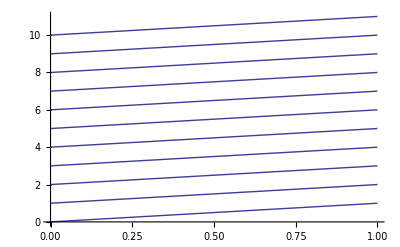

```mathematica
Show[Table[Plot[x+a,{x,0,1}],{a,0,10,1}],PlotRange->Automatic]
```